```mathematica
SetDirectory["/home/lukas/Dropbox/dev/tuberlin/epidemic-simulation/data"]
```

/home/lukas/Dropbox/dev/tuberlin/epidemic-simulation/data

One dimensional

```mathematica
Table[ simData[[c]] // Length, {c, 1, Length[simData] - 1}]
```

{8003,8003,8003,8003,8003,8003,8003,8003,8003,8003,8003,8003,8003,8003,4368}

```mathematica
simData = Import["sim_data.csv"];
simDataColumns = simData // Transpose;
```

```mathematica
numberOfRuns = 10;
RR = (Plus @@ Table[simDataColumns[[c]], {c, 11, Length[simDataColumns], 8}] // Rest) / numberOfRuns //N;

pInfection = simDataColumns[[1]];
RR = (Table[simDataColumns[[c]] // Rest, {c, 11, Length[simDataColumns], 8}] // Rest) ;

data = Table[ {pInfection[[1]], RR[[c]]} // Transpose,  {c, 1, Length[RR]}] // Join
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,226,0,0,0,9185,8903,9010,8917,9210,9359,9429,3,9535,9590,9586,9618,9724,9776,1,9831,9808,9852,9878,9901,9901,9913,9939,9945,9959,9941,9965,9972,9977,9985,9980,9992,9987,9988,9994,9994,9995,9999,10000,9998,9999,10000,10000,10000,10000,10000,10000,10000,10000,10000}

{{{0,0},{0.01,0},{0.02,0},{0.03,0},{0.04,0},{0.05,0},{0.06,0},{0.07,0},{0.08,0},{0.09,0},{0.1,0},{0.11,0},{0.12,0},74,{0.87,10000},{0.88,9998},{0.89,9998},{0.9,9999},{0.91,10000},{0.92,10000},{0.93,10000},{0.94,10000},{0.95,10000},{0.96,10000},{0.97,10000},{0.98,10000},{0.99,10000}},998}
 |  |  |  |

```mathematica
data
```

{{{0,0},{0.01,0},{0.02,0},{0.03,0},{0.04,0},{0.05,0},{0.06,0},{0.07,0},{0.08,0},{0.09,0},{0.1,0},{0.11,0},{0.12,0},74,{0.87,10000},{0.88,9998},{0.89,9998},{0.9,9999},{0.91,10000},{0.92,10000},{0.93,10000},{0.94,10000},{0.95,10000},{0.96,10000},{0.97,10000},{0.98,10000},{0.99,10000}},998}
 |  |  |  |

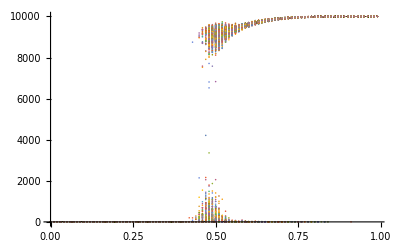

```mathematica
ListPlot[ data]
```

```mathematica
RR
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,6.1,1.7,3667.4,10605.9,18231.,15614.2,19001.7,22632.7,30097.6,30245.4,30175.4,34198.7,34350.9,38338.7,27004.6,38685.4,38876.9,38981.4,35217.1,39235.6,35405.6,35491.,35560.5,39575.,39634.9,39695.7,39740.5,39784.1,39825.7,39854.,39877.4,39903.,39914.4,39930.9,39944.8,39957.2,39965.8,39973.7,39977.3,39982.1,39987.1,39991.,39994.9,39994.6,39996.5,39997.8,39999.3,39999.1,39999.6,39999.5,40000.,40000.,40000.,40000.}

Two dimensional

```mathematica
simData = Import["sim_data_2d.csv"];
simDataColumns = simData // Transpose;
```

```mathematica
numberOfRuns = 100;
di = 0.1;
dc = 0.1;
minI = 0;
maxI = 1;
minC = 0;
maxC = 1;

extractRR[d_] := (Plus @@ Table[  d[[c]] , {c, 11, Length[d], 8}] ) / numberOfRuns //N;

dat = Table[  extractRR[Select[simData, #[[1]] == i && #[[2]] == c &][[1]] ], {i, minI, maxI, di}, {c, minC, maxC, dc}];
```

```mathematica
ListPlot3D[dat]
```

-Graphics3D-